# LiH

distance 1.6145

## Modules

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nqubits,nterms}=FormatHamiltonian["~/vqe/molecules/LiH/lih.txt"];
```

```mathematica
{nqubits,nterms}
```

{631,12}

```mathematica
groundstate=Min@Eigenvalues@CalcPauliSumMatrix@hamiltonian
```

-7.88206

```mathematica
groundstate=-7.882059857867098
```

-7.88206

## The runs

Trial 1

Tue 1 Feb 2022 15:28:30GMT

target: -7.88206

@cycle1, fev:1012, <E>: -7.876095442835334 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 44, 0}

@cycle2, fev:1699, <E>: -7.878039340461649 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 63, 25, 55, 0}

@cycle3, fev:2907, <E>: -7.880433315369665 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 83, 39, 62, 0}

@cycle4, fev:4984, <E>: -7.880733614941139 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 102, 56, 69, 0}

@cycle5, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 5

@cycle5, fev:5544, <E>: -7.880733614941139 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 102, 56, 69, 0}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 6

@cycle6, fev:6465, <E>: -7.880733614941139 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 102, 56, 69, 0}

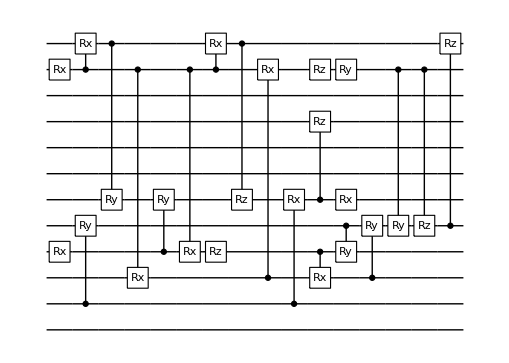

runtime=0.988189 hours

nansatz=23

nansatz/cycle={0,8,7,16,23,23}

<E>/cycle={-7.86136,-7.8761,-7.87804,-7.88043,-7.88073,-7.88073}

ϵ/cycle={0.0207014,0.00596442,0.00402052,0.00162654,0.00132624,0.00132602}

<E>=-7.88073

<E>-E_gs=0.00132602

Trial 2

Tue 1 Feb 2022 16:27:47GMT

target: -7.88206

@cycle1, fev:786, <E>: -7.876115106516198 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 73, 0}

@cycle2, fev:1782, <E>: -7.878039255942735 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 28, 29, 81, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 3

@cycle3, fev:2109, <E>: -7.878039255942735 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 28, 29, 81, 0}

I'm slowing down. Number of gates is increased to 72 @cycle 4

@cycle4, fev:2699, <E>: -7.878039255942735 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 28, 29, 81, 0}

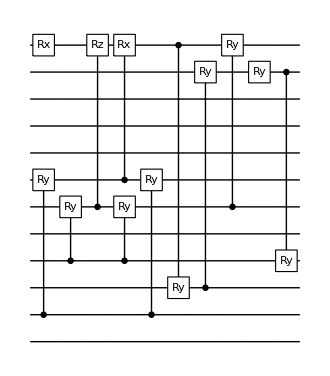

runtime=0.396703 hours

nansatz=12

nansatz/cycle={0,10,12,12}

<E>/cycle={-7.86136,-7.87612,-7.87804,-7.87804}

ϵ/cycle={0.0207014,0.00594475,0.0040206,0.0040206}

<E>=-7.87804

<E>-E_gs=0.0040206

Trial 3

Tue 1 Feb 2022 16:51:35GMT

target: -7.88206

@cycle1, fev:813, <E>: -7.862177814742154 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 53, 0, 41, 0}

@cycle2, fev:1488, <E>: -7.86383935982435 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 75, 0, 65, 0}

@cycle3, fev:2251, <E>: -7.878005762481465 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 122, 0, 69, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 4

@cycle4, fev:2610, <E>: -7.878005762481465 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 122, 0, 69, 0}

@cycle5, fev:3640, <E>: -7.8797852282550505 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 161, 0, 86, 1}

@cycle6, fev:5340, <E>: -7.88044244898844 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 176, 28, 100, 0}

@cycle7, fev:7819, <E>: -7.880626594257313 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 195, 42, 118, 0}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 8

@cycle8, fev:8412, <E>: -7.880626594257313 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 195, 42, 118, 0}

I'm slowing down. Number of gates is increased to 87 @cycle 9

@cycle9, fev:8949, <E>: -7.880626594257313 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 195, 42, 118, 0}

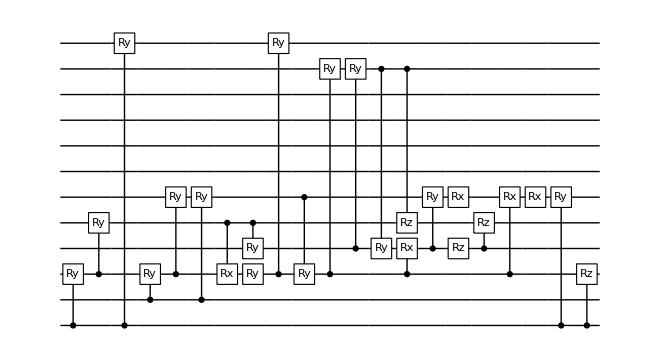

runtime=1.37136 hours

nansatz=24

nansatz/cycle={0,6,9,8,12,15,24,24}

<E>/cycle={-7.86136,-7.86218,-7.86384,-7.87801,-7.87979,-7.88044,-7.88063,-7.88063}

ϵ/cycle={0.0207014,0.019882,0.0182205,0.0040541,0.00227463,0.00161741,0.00143326,0.00143326}

<E>=-7.88063

<E>-E_gs=0.00143326

Trial 4

Tue 1 Feb 2022 18:13:52GMT

target: -7.88206

I'm slowing down. Number of gates is increased to 60 @cycle 1

@cycle1, fev:378, <E>: -7.861358505265061 nansatz: 0 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 0}

I'm slowing down. Number of gates is increased to 72 @cycle 2

@cycle2, fev:785, <E>: -7.861358505265061 nansatz: 0 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 0, 0}

-Graphics-

runtime=0.114451 hours

nansatz=0

nansatz/cycle={0,0}

<E>/cycle={-7.86136,-7.86136}

ϵ/cycle={0.0207014,0.0207014}

<E>=-7.86136

<E>-E_gs=0.0207014

Trial 5

Tue 1 Feb 2022 18:20:45GMT

target: -7.88206

@cycle1, fev:856, <E>: -7.878039463126886 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 25, 0, 66, 0}

I'm slowing down. Number of gates is increased to 60 @cycle 2

@cycle2, fev:1142, <E>: -7.878039463126886 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 25, 0, 66, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 3

@cycle3, fev:1672, <E>: -7.878039463126886 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 25, 0, 66, 1}

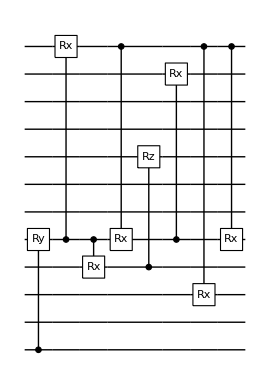

runtime=0.233075 hours

nansatz=8

nansatz/cycle={0,8,8}

<E>/cycle={-7.86136,-7.87804,-7.87804}

ϵ/cycle={0.0207014,0.00402039,0.00402039}

<E>=-7.87804

<E>-E_gs=0.00402039

Trial 6

Tue 1 Feb 2022 18:34:44GMT

target: -7.88206

@cycle1, fev:1181, <E>: -7.878072375081505 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 29, 46, 15, 2}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 2

@cycle2, fev:1716, <E>: -7.878072375081505 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 29, 46, 15, 1}

@cycle3, fev:3167, <E>: -7.878412333976561 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 56, 46, 46, 0}

@cycle4, fev:4556, <E>: -7.880394736631256 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 74, 71, 60, 0}

@cycle5, fev:6742, <E>: -7.880617232954423 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 92, 92, 75, 0}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 6

@cycle6, fev:7227, <E>: -7.880617232954423 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 92, 92, 75, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 87 @cycle 7

@cycle7, fev:8050, <E>: -7.880617232954423 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 92, 92, 75, 2}

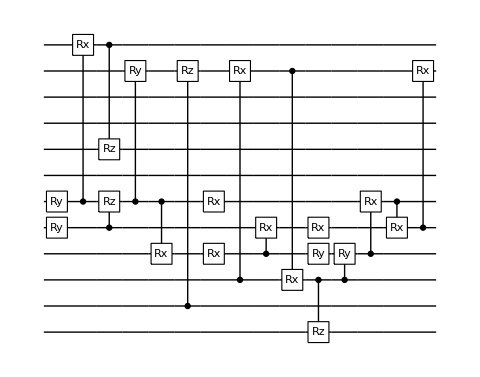

runtime=1.06737 hours

nansatz=20

nansatz/cycle={0,10,12,15,20,20}

<E>/cycle={-7.86136,-7.87807,-7.87841,-7.88039,-7.88062,-7.88062}

ϵ/cycle={0.0207014,0.00398748,0.00364752,0.00166512,0.00144262,0.00144262}

<E>=-7.88062

<E>-E_gs=0.00144262

Trial 7

Tue 1 Feb 2022 19:38:46GMT

target: -7.88206

@cycle1, fev:726, <E>: -7.876095361535506 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 15, 56, 20, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 2

@cycle2, fev:1079, <E>: -7.876095361535506 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 15, 56, 20, 0}

@cycle3, fev:2316, <E>: -7.878039347204737 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 32, 80, 37, 1}

@cycle4, fev:3510, <E>: -7.879095176817485 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 68, 80, 56, 0}

@cycle5, fev:5260, <E>: -7.880451182538964 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 98, 100, 64, 0}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 6

@cycle6, fev:5610, <E>: -7.880451182538964 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 98, 100, 64, 0}

@cycle7, pathetic result.

I'm slowing down. Number of gates is increased to 87 @cycle 7

@cycle7, fev:6398, <E>: -7.880451182538964 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 98, 100, 64, 1}

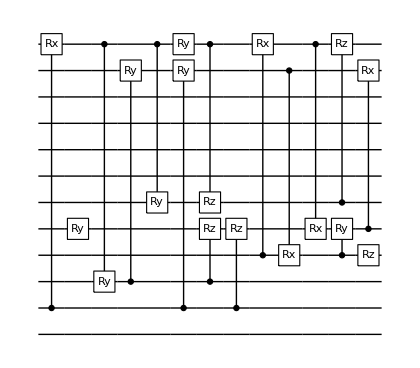

runtime=0.895507 hours

nansatz=17

nansatz/cycle={0,8,10,15,17,17}

<E>/cycle={-7.86136,-7.8761,-7.87804,-7.8791,-7.88045,-7.88045}

ϵ/cycle={0.0207014,0.0059645,0.00402051,0.00296468,0.00160868,0.00160868}

<E>=-7.88045

<E>-E_gs=0.00160868

Trial 8

Tue 1 Feb 2022 20:32:30GMT

target: -7.88206

@cycle1, fev:848, <E>: -7.876097738639887 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 20, 53, 20, 0}

@cycle2, fev:2009, <E>: -7.878040797391751 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 43, 53, 45, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 3

@cycle3, fev:2380, <E>: -7.878040797391751 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 43, 53, 45, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 4

@cycle4, fev:2960, <E>: -7.878040797391751 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 43, 53, 45, 0}

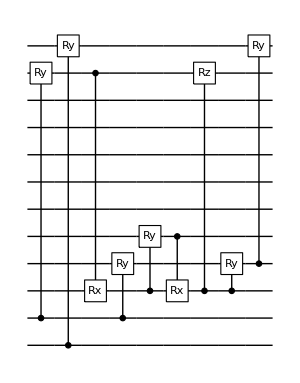

runtime=0.419435 hours

nansatz=9

nansatz/cycle={0,7,9,9}

<E>/cycle={-7.86136,-7.8761,-7.87804,-7.87804}

ϵ/cycle={0.0207014,0.00596212,0.00401906,0.00401906}

<E>=-7.87804

<E>-E_gs=0.00401906

Trial 9

Tue 1 Feb 2022 20:57:40GMT

target: -7.88206

@cycle1, fev:1265, <E>: -7.876095790649055 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 63, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 2

@cycle2, fev:1729, <E>: -7.876095790649055 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 27, 0, 63, 0}

@cycle3, fev:3248, <E>: -7.876695558110462 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 98, 0}

@cycle4, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 4

@cycle4, fev:3894, <E>: -7.876695558110462 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 48, 0, 98, 0}

@cycle5, fev:5910, <E>: -7.8785890810103885 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 74, 0, 139, 0}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 87 @cycle 6

@cycle6, fev:6784, <E>: -7.8785890810103885 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 74, 0, 139, 0}

@cycle7, fev:9044, <E>: -7.880248737128029 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 111, 0, 186, 1}

@cycle8, fev:12523, <E>: -7.8810435369067395 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 148, 18, 213, 1}

@cycle9, fev:16682, <E>: -7.881238070531124 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 191, 18, 246, 0}

@cycle10, pathetic result.

I'm slowing down. Number of gates is increased to 105 @cycle 10

@cycle10, fev:17959, <E>: -7.881238070531124 nansatz: 36 merged-smallθ-metric-bf-gmerged: {1, 191, 18, 246, 0}

@cycle11, fev:22500, <E>: -7.881555911612695 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 229, 18, 313, 2}

@cycle12, pathetic result.

I'm slowing down. Number of gates is increased to 126 @cycle 12

@cycle12, fev:23749, <E>: -7.881555911612695 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 229, 18, 313, 0}

@cycle13, pathetic result.

I'm slowing down. Number of gates is increased to 152 @cycle 13

@cycle13, fev:25039, <E>: -7.881555911612695 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 229, 18, 313, 0}

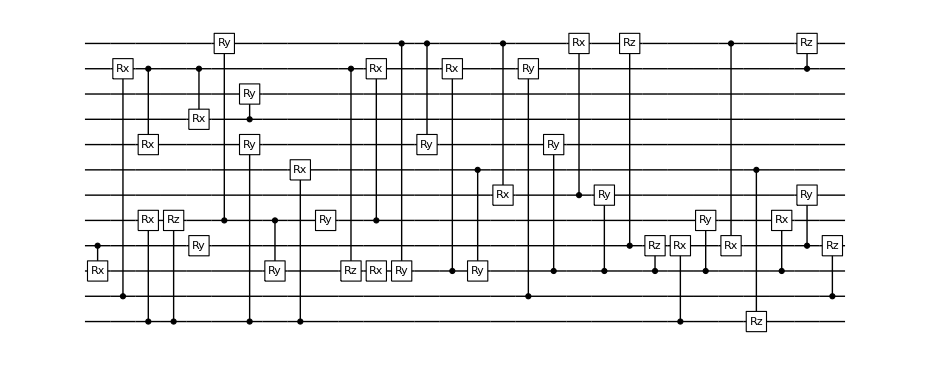

runtime=4.62053 hours

nansatz=35

nansatz/cycle={0,10,13,18,21,26,36,35,35}

<E>/cycle={-7.86136,-7.8761,-7.8767,-7.87859,-7.88025,-7.88104,-7.88124,-7.88156,-7.88156}

ϵ/cycle={0.0207014,0.00596407,0.0053643,0.00347078,0.00181112,0.00101632,0.000821787,0.000503946,0.000503547}

<E>=-7.88156

<E>-E_gs=0.000503547

Trial 10

Wed 2 Feb 2022 01:34:54GMT

target: -7.88206

@cycle1, fev:1722, <E>: -7.876197686653262 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 25, 43, 15, 0}

@cycle2, fev:2919, <E>: -7.8780393715254124 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 52, 43, 44, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 60 @cycle 3

@cycle3, fev:3210, <E>: -7.8780393715254124 nansatz: 11 merged-smallθ-metric-bf-gmerged: {0, 52, 43, 44, 0}

@cycle4, fev:4510, <E>: -7.878632562464832 nansatz: 15 merged-smallθ-metric-bf-gmerged: {2, 82, 43, 68, 0}

@cycle5, fev:6072, <E>: -7.880876882427666 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 118, 43, 87, 1}

@cycle6, pathetic result.

I'm slowing down. Number of gates is increased to 72 @cycle 6

@cycle6, fev:6425, <E>: -7.880876882427666 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 118, 43, 87, 0}

@cycle7, fev:8827, <E>: -7.88106381310819 nansatz: 23 merged-smallθ-metric-bf-gmerged: {2, 156, 43, 117, 1}

@cycle8, pathetic result.

I'm slowing down. Number of gates is increased to 87 @cycle 8

@cycle8, fev:9575, <E>: -7.88106381310819 nansatz: 23 merged-smallθ-metric-bf-gmerged: {2, 156, 43, 117, 0}

@cycle9, pathetic result.

I'm slowing down. Number of gates is increased to 105 @cycle 9

@cycle9, fev:10606, <E>: -7.88106381310819 nansatz: 23 merged-smallθ-metric-bf-gmerged: {2, 156, 43, 117, 0}

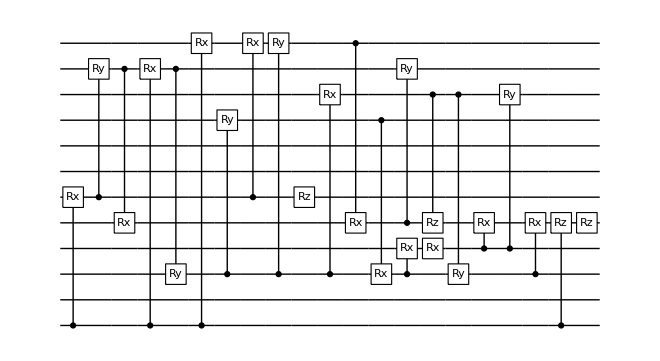

runtime=1.56846 hours

nansatz=23

nansatz/cycle={0,17,11,15,20,23,23}

<E>/cycle={-7.86136,-7.8762,-7.87804,-7.87863,-7.88088,-7.88106,-7.88106}

ϵ/cycle={0.0207014,0.00586217,0.00402049,0.0034273,0.00118298,0.000996045,0.000995581}

<E>=-7.88106

<E>-E_gs=0.000995581

{-7.88073,-7.87804,-7.88063,-7.86136,-7.87804,-7.88062,-7.88045,-7.87804,-7.88156,-7.88106}

```mathematica
results={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
DestroyAllQuregs[];
conf=DefaultConfig[12];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[12,hamiltonian,conf]];

Print@DrawCircuit[ansatz,12];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[12,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
DestroyAllQuregs[];
AppendTo[results,{ansatz,θvars,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

## Total results

```mathematica
{ψ,ψwork}=CreateQuregs[12,2];
ansatzinit=Subscript[X, #]&/@Range[0,3];
chemacc=1.59*10^-3;
trial=1;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦3⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp1,{"trial","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
```

```mathematica
disp1//TableForm
```

trial | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
1 | True | 0.00132602 | 23 | {0, 102, 56, 69} | 7112 | {0, 8, 7, 16, 23, 23} | {}
2 | False | 0.0040206 | 12 | {0, 28, 29, 81} | 2938 | {0, 10, 12, 12} | {4}
3 | True | 0.00143326 | 24 | {1, 195, 42, 118} | 9580 | {0, 6, 9, 8, 12, 15, 24, 24} | {9}
4 | False | 0.0207014 | 0 | {0, 0, 0, 0} | 785 | {0, 0} | {1, 2}
5 | False | 0.00402039 | 8 | {1, 25, 0, 66} | 1801 | {0, 8, 8} | {2}
6 | True | 0.00144262 | 20 | {1, 92, 92, 75} | 8606 | {0, 10, 12, 15, 20, 20} | {}
7 | False | 0.00160868 | 17 | {1, 98, 100, 64} | 6754 | {0, 8, 10, 15, 17, 17} | {}
8 | False | 0.00401906 | 9 | {0, 43, 53, 45} | 3172 | {0, 7, 9, 9} | {}
9 | True | 0.000503547 | 35 | {1, 229, 18, 313} | 25909 | {0, 10, 13, 18, 21, 26, 36, 35, 35} | {}
10 | True | 0.000995581 | 23 | {2, 156, 43, 117} | 11145 | {0, 17, 11, 15, 20, 23, 23} | {}

```mathematica
results
```

{{{Rx_10[θ_117],Rx_3[θ_204],C_1[Ry_4[θ_173]],C_10[Rx_11[θ_129]],C_11[Ry_5[θ_108]],C_10[Rx_2[θ_30]],C_3[Ry_5[θ_206]],C_10[Rx_3[θ_99]],Rz_3[θ_180],C_10[Rx_11[θ_104]],C_11[Rz_5[θ_194]],C_2[Rx_10[θ_235]],C_1[Rx_5[θ_207]],C_3[Rx_2[θ_232]],Rz_10[θ_223],C_5[Rz_8[θ_211]],Ry_10[θ_155],C_4[Ry_3[θ_228]],Rx_5[θ_236],C_2[Ry_4[θ_181]],C_10[Ry_4[θ_185]],C_10[Rz_4[θ_188]],C_4[Rz_11[θ_197]]},<|θ_30→3.14171,θ_99→3.13908,θ_104→4.23595,θ_108→-1.76848,θ_117→0.297975,θ_129→4.70924,θ_155→-0.981542,θ_173→-3.14159,θ_180→-1.56917,θ_181→3.14159,θ_185→3.14159,θ_188→-3.1601,θ_194→3.15338,θ_197→3.14435,θ_204→-0.339249,θ_206→0.337498,θ_207→1.50693,θ_211→0.652931,θ_223→-1.57076,θ_228→-0.337543,θ_232→-0.0618515,θ_235→-0.98185,θ_236→-1.5097|>,<|ansatz→{{},{C_3[Ry_5[θ_9]],C_0[Rx_4[θ_22]],C_1[Rx_10[θ_24]],Ry_5[θ_16],Rx_4[θ_23],C_10[Rx_2[θ_30]],C_10[Rx_11[θ_83]],C_10[Rx_3[θ_99]]},{Rx_10[θ_117],C_10[Rx_11[θ_129]],C_11[Ry_5[θ_108]],C_5[Rz_10[θ_111]],C_10[Rx_2[θ_30]],C_10[Rx_3[θ_99]],C_10[Rx_11[θ_104]]},{Rx_10[θ_117],C_1[Ry_4[θ_173]],C_10[Rx_11[θ_129]],C_11[Ry_5[θ_108]],C_10[Rx_2[θ_30]],C_10[Rx_3[θ_99]],C_10[Rx_11[θ_104]],Rz_3[θ_180],C_2[Ry_10[θ_151]],C_11[Rz_5[θ_194]],Ry_10[θ_155],C_2[Rz_0[θ_171]],C_2[Ry_4[θ_181]],C_10[Ry_4[θ_185]],C_10[Rz_4[θ_188]],C_4[Rz_11[θ_197]]},{Rx_10[θ_117],Rx_3[θ_204],C_1[Ry_4[θ_173]],C_10[Rx_11[θ_129]],C_11[Ry_5[θ_108]],C_10[Rx_2[θ_30]],C_3[Ry_5[θ_206]],C_10[Rx_3[θ_99]],Rz_3[θ_180],C_10[Rx_11[θ_104]],C_11[Rz_5[θ_194]],C_2[Rx_10[θ_235]],C_1[Rx_5[θ_207]],C_3[Rx_2[θ_232]],Rz_10[θ_223],C_5[Rz_8[θ_211]],Ry_10[θ_155],C_4[Ry_3[θ_228]],Rx_5[θ_236],C_2[Ry_4[θ_181]],C_10[Ry_4[θ_185]],C_10[Rz_4[θ_188]],C_4[Rz_11[θ_197]]},{Rx_10[θ_117],Rx_3[θ_204],C_1[Ry_4[θ_173]],C_10[Rx_11[θ_129]],C_11[Ry_5[θ_108]],C_10[Rx_2[θ_30]],C_3[Ry_5[θ_206]],C_10[Rx_3[θ_99]],Rz_3[θ_180],C_10[Rx_11[θ_104]],C_11[Rz_5[θ_194]],C_2[Rx_10[θ_235]],C_1[Rx_5[θ_207]],C_3[Rx_2[θ_232]],Rz_10[θ_223],C_5[Rz_8[θ_211]],Ry_10[θ_155],C_4[Ry_3[θ_228]],Rx_5[θ_236],C_2[Ry_4[θ_181]],C_10[Ry_4[θ_185]],C_10[Rz_4[θ_188]],C_4[Rz_11[θ_197]]}},θvars→{<||>,<|θ_9→-0.382918,θ_16→0.382754,θ_22→0.163511,θ_23→-0.163273,θ_24→-0.237626,θ_30→3.14166,θ_83→3.14158,θ_99→3.14159|>,<|θ_30→3.14159,θ_99→3.14157,θ_104→3.13179,θ_108→-3.16015,θ_111→3.14191,θ_117→0.259574,θ_129→5.45713|>,<|θ_30→3.14155,θ_99→3.14159,θ_104→3.14159,θ_108→-3.14159,θ_117→0.290408,θ_129→5.40729,θ_151→0.876462,θ_155→-0.876427,θ_171→2.89497,θ_173→-3.14159,θ_180→-1.43716,θ_181→3.14159,θ_185→3.14159,θ_188→-3.1539,θ_194→3.13007,θ_197→3.14479|>,<|θ_30→3.14226,θ_99→3.13913,θ_104→4.23308,θ_108→-1.76993,θ_117→0.297669,θ_129→4.71122,θ_155→-0.981544,θ_173→-3.14159,θ_180→-1.56927,θ_181→3.14159,θ_185→3.14159,θ_188→-3.16031,θ_194→3.15342,θ_197→3.14437,θ_204→-0.340835,θ_206→0.336574,θ_207→1.5067,θ_211→0.65127,θ_223→-1.5707,θ_228→-0.339136,θ_232→-0.0617476,θ_235→-0.981813,θ_236→-1.5093|>,<|θ_30→3.14171,θ_99→3.13908,θ_104→4.23595,θ_108→-1.76848,θ_117→0.297975,θ_129→4.70924,θ_155→-0.981542,θ_173→-3.14159,θ_180→-1.56917,θ_181→3.14159,θ_185→3.14159,θ_188→-3.1601,θ_194→3.15338,θ_197→3.14435,θ_204→-0.339249,θ_206→0.337498,θ_207→1.50693,θ_211→0.652931,θ_223→-1.57076,θ_228→-0.337543,θ_232→-0.0618515,θ_235→-0.98185,θ_236→-1.5097|>},E→{-7.86136,-7.8761,-7.87804,-7.88043,-7.88073,-7.88073},idx→{1,101,151,201,251,251}|>,7112,{},{0,102,56,69}},{{Rx_11[θ_119],C_1[Ry_6[θ_10]],C_3[Ry_5[θ_116]],C_5[Rz_11[θ_133]],C_6[Rx_11[θ_18]],C_3[Ry_5[θ_22]],C_1[Ry_6[θ_59]],C_11[Ry_2[θ_36]],C_2[Ry_10[θ_50]],C_5[Ry_11[θ_66]],Ry_10[θ_51],C_10[Ry_3[θ_87]]},<|θ_10→3.14159,θ_18→-1.56507,θ_22→2.31955,θ_36→-3.14159,θ_50→-3.14159,θ_51→3.14159,θ_59→-3.14159,θ_66→3.14159,θ_87→3.14159,θ_116→-2.32691,θ_119→1.56522,θ_133→0.283919|>,<|ansatz→{{},{C_1[Ry_6[θ_10]],C_3[Ry_5[θ_22]],C_6[Rx_11[θ_18]],C_1[Ry_6[θ_59]],C_11[Ry_2[θ_36]],C_2[Ry_10[θ_50]],C_5[Ry_11[θ_66]],Ry_10[θ_51],C_10[Ry_3[θ_87]],Rz_3[θ_99]},{Rx_11[θ_119],C_1[Ry_6[θ_10]],C_3[Ry_5[θ_116]],C_5[Rz_11[θ_133]],C_6[Rx_11[θ_18]],C_3[Ry_5[θ_22]],C_1[Ry_6[θ_59]],C_11[Ry_2[θ_36]],C_2[Ry_10[θ_50]],C_5[Ry_11[θ_66]],Ry_10[θ_51],C_10[Ry_3[θ_87]]},{Rx_11[θ_119],C_1[Ry_6[θ_10]],C_3[Ry_5[θ_116]],C_5[Rz_11[θ_133]],C_6[Rx_11[θ_18]],C_3[Ry_5[θ_22]],C_1[Ry_6[θ_59]],C_11[Ry_2[θ_36]],C_2[Ry_10[θ_50]],C_5[Ry_11[θ_66]],Ry_10[θ_51],C_10[Ry_3[θ_87]]}},θvars→{<||>,<|θ_10→3.14159,θ_18→-0.237843,θ_22→-0.0143598,θ_36→-3.14159,θ_50→-3.14159,θ_51→3.14159,θ_59→-3.14159,θ_66→3.14159,θ_87→3.14159,θ_99→1.5686|>,<|θ_10→3.14159,θ_18→-1.56507,θ_22→2.31955,θ_36→-3.14159,θ_50→-3.14159,θ_51→3.14159,θ_59→-3.14159,θ_66→3.14159,θ_87→3.14159,θ_116→-2.32691,θ_119→1.56522,θ_133→0.283919|>,<|θ_10→3.14159,θ_18→-1.56507,θ_22→2.31955,θ_36→-3.14159,θ_50→-3.14159,θ_51→3.14159,θ_59→-3.14159,θ_66→3.14159,θ_87→3.14159,θ_116→-2.32691,θ_119→1.56522,θ_133→0.283919|>},E→{-7.86136,-7.87612,-7.87804,-7.87804},idx→{1,101,151,151}|>,2938,{4},{0,28,29,81}},{{C_0[Ry_2[θ_282]],C_2[Ry_4[θ_285]],C_0[Ry_11[θ_189]],C_1[Ry_2[θ_295]],C_2[Ry_5[θ_297]],C_1[Ry_5[θ_107]],C_4[Rx_2[θ_228]],C_4[Ry_3[θ_247]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]],C_10[Rz_4[θ_328]],C_2[Rx_3[θ_333]],C_3[Ry_5[θ_335]],Rz_3[θ_340],Rx_5[θ_349],C_3[Rz_4[θ_375]],C_2[Rx_5[θ_363]],Rx_5[θ_369],C_0[Ry_5[θ_377]],C_0[Rz_2[θ_378]]},<|θ_107→3.50897,θ_120→-3.14159,θ_125→-3.14159,θ_130→3.14159,θ_148→3.14305,θ_173→-0.234836,θ_176→3.14159,θ_189→-3.14159,θ_228→-3.14114,θ_247→3.14159,θ_282→-1.12003,θ_285→-0.150407,θ_295→1.13746,θ_297→-3.38662,θ_328→-3.14003,θ_333→0.0723628,θ_335→3.14159,θ_340→4.17622,θ_349→-1.57075,θ_363→3.1416,θ_369→-1.57083,θ_375→5.29252,θ_377→-3.14159,θ_378→-1.5312|>,<|ansatz→{{},{Ry_10[θ_68],Rx_7[θ_59],C_2[Ry_10[θ_16]],C_7[Ry_6[θ_100]],C_6[Rx_2[θ_29]],C_7[Ry_3[θ_44]]},{Rx_7[θ_59],C_1[Ry_5[θ_107]],C_7[Ry_6[θ_100]],C_6[Rx_2[θ_29]],C_7[Ry_3[θ_44]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]]},{C_0[Ry_11[θ_189]],C_1[Ry_5[θ_107]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]]},{Ry_4[θ_218],C_1[Ry_5[θ_107]],C_4[Rx_2[θ_228]],C_0[Rz_2[θ_243]],C_4[Ry_3[θ_247]],C_0[Ry_11[θ_189]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]]},{C_0[Ry_2[θ_282]],C_2[Ry_4[θ_285]],C_1[Ry_2[θ_295]],C_0[Rz_4[θ_293]],C_2[Ry_5[θ_297]],C_0[Ry_11[θ_189]],C_1[Ry_5[θ_107]],C_4[Rx_2[θ_228]],C_4[Ry_3[θ_247]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]]},{C_0[Ry_2[θ_282]],C_2[Ry_4[θ_285]],C_0[Ry_11[θ_189]],C_1[Ry_2[θ_295]],C_2[Ry_5[θ_297]],C_1[Ry_5[θ_107]],C_4[Rx_2[θ_228]],C_4[Ry_3[θ_247]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]],C_10[Rz_4[θ_328]],C_2[Rx_3[θ_333]],C_3[Ry_5[θ_335]],Rz_3[θ_340],Rx_5[θ_349],C_3[Rz_4[θ_375]],C_2[Rx_5[θ_363]],Rx_5[θ_369],C_0[Ry_5[θ_377]],C_0[Rz_2[θ_378]]},{C_0[Ry_2[θ_282]],C_2[Ry_4[θ_285]],C_0[Ry_11[θ_189]],C_1[Ry_2[θ_295]],C_2[Ry_5[θ_297]],C_1[Ry_5[θ_107]],C_4[Rx_2[θ_228]],C_4[Ry_3[θ_247]],Ry_2[θ_173],C_2[Ry_11[θ_176]],C_5[Ry_2[θ_120]],C_2[Ry_10[θ_125]],C_3[Ry_10[θ_130]],C_10[Ry_3[θ_148]],C_10[Rz_4[θ_328]],C_2[Rx_3[θ_333]],C_3[Ry_5[θ_335]],Rz_3[θ_340],Rx_5[θ_349],C_3[Rz_4[θ_375]],C_2[Rx_5[θ_363]],Rx_5[θ_369],C_0[Ry_5[θ_377]],C_0[Rz_2[θ_378]]}},θvars→{<||>,<|θ_16→-0.205075,θ_29→-3.14159,θ_44→3.14159,θ_59→-0.0694679,θ_68→0.205075,θ_100→-3.1951|>,<|θ_29→-3.14159,θ_44→3.14159,θ_59→-0.0690437,θ_100→-3.14159,θ_107→0.0977533,θ_120→-3.139,θ_125→-3.14051,θ_130→3.14051,θ_148→3.14153|>,<|θ_107→0.105525,θ_120→-3.14159,θ_125→-3.14284,θ_130→3.1419,θ_148→3.14166,θ_173→0.238083,θ_176→3.14157,θ_189→-3.14157|>,<|θ_107→0.0979981,θ_120→-3.14695,θ_125→-3.14159,θ_130→3.14159,θ_148→3.14154,θ_173→0.243667,θ_176→3.1416,θ_189→-3.14161,θ_218→-0.0989323,θ_228→-2.94824,θ_243→-1.59193,θ_247→3.14159|>,<|θ_107→3.54655,θ_120→-3.14159,θ_125→-3.14159,θ_130→3.14159,θ_148→3.14159,θ_173→0.2345,θ_176→3.14159,θ_189→-3.14159,θ_228→-3.1493,θ_247→3.14159,θ_282→1.01348,θ_285→-0.141455,θ_293→1.62661,θ_295→-1.02857,θ_297→-3.43859|>,<|θ_107→3.50897,θ_120→-3.14159,θ_125→-3.14159,θ_130→3.14159,θ_148→3.14305,θ_173→-0.234836,θ_176→3.14159,θ_189→-3.14159,θ_228→-3.14114,θ_247→3.14159,θ_282→-1.12003,θ_285→-0.150407,θ_295→1.13746,θ_297→-3.38662,θ_328→-3.14003,θ_333→0.0723628,θ_335→3.14159,θ_340→4.17622,θ_349→-1.57075,θ_363→3.1416,θ_369→-1.57083,θ_375→5.29252,θ_377→-3.14159,θ_378→-1.5312|>,<|θ_107→3.50897,θ_120→-3.14159,θ_125→-3.14159,θ_130→3.14159,θ_148→3.14305,θ_173→-0.234836,θ_176→3.14159,θ_189→-3.14159,θ_228→-3.14114,θ_247→3.14159,θ_282→-1.12003,θ_285→-0.150407,θ_295→1.13746,θ_297→-3.38662,θ_328→-3.14003,θ_333→0.0723628,θ_335→3.14159,θ_340→4.17622,θ_349→-1.57075,θ_363→3.1416,θ_369→-1.57083,θ_375→5.29252,θ_377→-3.14159,θ_378→-1.5312|>},E→{-7.86136,-7.86218,-7.86384,-7.87801,-7.87979,-7.88044,-7.88063,-7.88063},idx→{1,101,151,201,261,321,381,381}|>,9580,{9},{1,195,42,118}},{{},<||>,<|ansatz→{{},{}},θvars→{<||>,<||>},E→{-7.86136,-7.86136},idx→{1,1}|>,785,{1,2},{0,0,0,0}},{{C_0[Ry_4[θ_33]],C_4[Rx_11[θ_44]],C_4[Rx_3[θ_48]],C_11[Rx_4[θ_51]],C_3[Rz_7[θ_94]],C_4[Rx_10[θ_63]],C_11[Rx_2[θ_82]],C_11[Rx_4[θ_98]]},<|θ_33→0.259873,θ_44→3.14159,θ_48→-3.14159,θ_51→-0.82475,θ_63→3.14159,θ_82→-3.14159,θ_94→-3.14161,θ_98→3.14159|>,<|ansatz→{{},{C_0[Ry_4[θ_33]],C_4[Rx_11[θ_44]],C_4[Rx_3[θ_48]],C_11[Rx_4[θ_51]],C_3[Rz_7[θ_94]],C_4[Rx_10[θ_63]],C_11[Rx_2[θ_82]],C_11[Rx_4[θ_98]]},{C_0[Ry_4[θ_33]],C_4[Rx_11[θ_44]],C_4[Rx_3[θ_48]],C_11[Rx_4[θ_51]],C_3[Rz_7[θ_94]],C_4[Rx_10[θ_63]],C_11[Rx_2[θ_82]],C_11[Rx_4[θ_98]]}},θvars→{<||>,<|θ_33→0.259873,θ_44→3.14159,θ_48→-3.14159,θ_51→-0.82475,θ_63→3.14159,θ_82→-3.14159,θ_94→-3.14161,θ_98→3.14159|>,<|θ_33→0.259873,θ_44→3.14159,θ_48→-3.14159,θ_51→-0.82475,θ_63→3.14159,θ_82→-3.14159,θ_94→-3.14161,θ_98→3.14159|>},E→{-7.86136,-7.87804,-7.87804},idx→{1,101,101}|>,1801,{2},{1,25,0,66}},{{Ry_4[θ_195],Ry_5[θ_49],C_5[Rx_11[θ_76]],C_4[Rz_5[θ_219]],C_11[Rz_7[θ_250]],C_5[Ry_10[θ_69]],C_5[Rx_3[θ_233]],C_1[Rz_10[θ_243]],Rx_5[θ_7],Rx_3[θ_246],C_2[Rx_10[θ_5]],C_3[Rx_4[θ_230]],C_10[Rx_2[θ_95]],Rx_4[θ_267],Ry_3[θ_278],C_2[Rz_0[θ_164]],C_2[Ry_3[θ_275]],C_3[Rx_5[θ_4]],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]},<|θ_4→-3.14159,θ_5→-0.141451,θ_7→3.14159,θ_49→0.259126,θ_69→3.01332,θ_76→3.14159,θ_95→-3.1451,θ_113→-1.004,θ_123→3.14165,θ_164→3.09742,θ_195→-0.427556,θ_219→3.14228,θ_230→-0.980303,θ_233→0.0750935,θ_243→2.01433,θ_246→-0.0732942,θ_250→-2.20992,θ_267→1.40785,θ_275→-3.1356,θ_278→3.13702|>,<|ansatz→{{},{Ry_5[θ_49],Rx_3[θ_28],C_5[Rx_11[θ_76]],C_5[Ry_10[θ_69]],C_2[Rx_10[θ_5]],Rx_5[θ_7],C_10[Rx_2[θ_95]],C_10[Rz_8[θ_59]],C_10[Ry_3[θ_100]],C_3[Rx_5[θ_4]]},{Ry_5[θ_49],Rx_3[θ_28],C_5[Rx_11[θ_76]],C_5[Ry_10[θ_69]],C_2[Rx_10[θ_5]],Rx_5[θ_7],C_10[Rx_2[θ_95]],C_10[Ry_3[θ_100]],C_3[Rx_5[θ_4]],Rz_10[θ_112],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]},{Ry_4[θ_195],Ry_5[θ_49],C_5[Rx_11[θ_76]],C_4[Rz_5[θ_219]],C_5[Ry_10[θ_69]],C_1[Rx_4[θ_162]],Rx_5[θ_7],C_2[Rx_10[θ_5]],C_10[Rx_2[θ_95]],C_10[Ry_3[θ_100]],C_2[Rz_0[θ_164]],Rz_10[θ_112],C_3[Rx_5[θ_4]],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]},{Ry_4[θ_195],Ry_5[θ_49],C_5[Rx_11[θ_76]],C_4[Rz_5[θ_219]],C_11[Rz_7[θ_250]],C_5[Ry_10[θ_69]],C_5[Rx_3[θ_233]],C_1[Rz_10[θ_243]],Rx_5[θ_7],Rx_3[θ_246],C_2[Rx_10[θ_5]],C_3[Rx_4[θ_230]],C_10[Rx_2[θ_95]],Rx_4[θ_267],Ry_3[θ_278],C_2[Rz_0[θ_164]],C_2[Ry_3[θ_275]],C_3[Rx_5[θ_4]],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]},{Ry_4[θ_195],Ry_5[θ_49],C_5[Rx_11[θ_76]],C_4[Rz_5[θ_219]],C_11[Rz_7[θ_250]],C_5[Ry_10[θ_69]],C_5[Rx_3[θ_233]],C_1[Rz_10[θ_243]],Rx_5[θ_7],Rx_3[θ_246],C_2[Rx_10[θ_5]],C_3[Rx_4[θ_230]],C_10[Rx_2[θ_95]],Rx_4[θ_267],Ry_3[θ_278],C_2[Rz_0[θ_164]],C_2[Ry_3[θ_275]],C_3[Rx_5[θ_4]],C_5[Rx_4[θ_113]],C_4[Rx_10[θ_123]]}},θvars→{<||>,<|θ_4→-3.14159,θ_5→-0.110535,θ_7→3.14187,θ_28→-0.040854,θ_49→-0.236671,θ_59→3.14269,θ_69→3.14179,θ_76→3.14145,θ_95→-3.14159,θ_100→3.14219|>,<|θ_4→-3.14159,θ_5→-0.124541,θ_7→3.14159,θ_28→-0.0384341,θ_49→-0.235548,θ_69→3.1432,θ_76→3.14159,θ_95→-3.14159,θ_100→3.14372,θ_112→-1.57082,θ_113→-0.682805,θ_123→3.14159|>,<|θ_4→-3.14159,θ_5→-0.121919,θ_7→3.14159,θ_49→-0.262701,θ_69→3.14172,θ_76→3.14159,θ_95→-3.14159,θ_100→3.14189,θ_112→-0.435682,θ_113→-1.00982,θ_123→3.14159,θ_162→0.423082,θ_164→2.27007,θ_195→-0.423095,θ_219→3.14159|>,<|θ_4→-3.14159,θ_5→-0.141451,θ_7→3.14159,θ_49→0.259126,θ_69→3.01332,θ_76→3.14159,θ_95→-3.1451,θ_113→-1.004,θ_123→3.14165,θ_164→3.09742,θ_195→-0.427556,θ_219→3.14228,θ_230→-0.980303,θ_233→0.0750935,θ_243→2.01433,θ_246→-0.0732942,θ_250→-2.20992,θ_267→1.40785,θ_275→-3.1356,θ_278→3.13702|>,<|θ_4→-3.14159,θ_5→-0.141451,θ_7→3.14159,θ_49→0.259126,θ_69→3.01332,θ_76→3.14159,θ_95→-3.1451,θ_113→-1.004,θ_123→3.14165,θ_164→3.09742,θ_195→-0.427556,θ_219→3.14228,θ_230→-0.980303,θ_233→0.0750935,θ_243→2.01433,θ_246→-0.0732942,θ_250→-2.20992,θ_267→1.40785,θ_275→-3.1356,θ_278→3.13702|>},E→{-7.86136,-7.87807,-7.87841,-7.88039,-7.88062,-7.88062},idx→{1,101,161,221,281,281}|>,8606,{},{1,92,92,75}},{{C_1[Rx_11[θ_12]],Ry_4[θ_184],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_11[Ry_5[θ_121]],Ry_11[θ_119],C_1[Ry_10[θ_95]],C_2[Rz_4[θ_262]],C_11[Rz_5[θ_144]],C_1[Rz_4[θ_228]],C_3[Rx_11[θ_245]],C_10[Rx_3[θ_99]],C_11[Rx_4[θ_252]],C_3[Ry_4[θ_193]],C_5[Rz_11[θ_213]],C_4[Rx_10[θ_197]],Rz_3[θ_195]},<|θ_12→0.29058,θ_21→3.17177,θ_32→-3.14159,θ_95→3.14159,θ_99→-3.14138,θ_119→-1.57102,θ_121→-0.884001,θ_144→-3.14957,θ_184→1.0218,θ_193→-1.02153,θ_195→2.35937,θ_197→-3.14159,θ_213→3.12922,θ_228→-1.57344,θ_245→-1.57128,θ_252→-1.87151,θ_262→1.57278|>,<|ansatz→{{},{C_1[Rx_11[θ_12]],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_10[Rz_1[θ_66]],C_2[Rz_8[θ_72]],C_10[Rz_7[θ_88]],C_1[Ry_10[θ_95]],C_10[Rx_3[θ_99]]},{C_1[Rx_11[θ_12]],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_11[Ry_5[θ_121]],Ry_11[θ_119],C_1[Ry_10[θ_95]],C_11[Rz_5[θ_144]],C_10[Rx_3[θ_99]],Ry_11[θ_131],C_1[Rx_11[θ_133]]},{C_1[Rx_11[θ_12]],Ry_4[θ_184],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_11[Ry_5[θ_121]],Ry_11[θ_119],C_1[Ry_10[θ_95]],C_11[Rz_5[θ_144]],C_10[Rx_3[θ_99]],C_1[Rx_11[θ_133]],C_3[Ry_4[θ_193]],C_5[Rz_11[θ_213]],Rz_3[θ_195],C_4[Rx_10[θ_197]],C_0[Rz_4[θ_206]]},{C_1[Rx_11[θ_12]],Ry_4[θ_184],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_11[Ry_5[θ_121]],Ry_11[θ_119],C_1[Ry_10[θ_95]],C_2[Rz_4[θ_262]],C_11[Rz_5[θ_144]],C_1[Rz_4[θ_228]],C_3[Rx_11[θ_245]],C_10[Rx_3[θ_99]],C_11[Rx_4[θ_252]],C_3[Ry_4[θ_193]],C_5[Rz_11[θ_213]],C_4[Rx_10[θ_197]],Rz_3[θ_195]},{C_1[Rx_11[θ_12]],Ry_4[θ_184],C_11[Ry_2[θ_21]],C_2[Ry_10[θ_32]],C_11[Ry_5[θ_121]],Ry_11[θ_119],C_1[Ry_10[θ_95]],C_2[Rz_4[θ_262]],C_11[Rz_5[θ_144]],C_1[Rz_4[θ_228]],C_3[Rx_11[θ_245]],C_10[Rx_3[θ_99]],C_11[Rx_4[θ_252]],C_3[Ry_4[θ_193]],C_5[Rz_11[θ_213]],C_4[Rx_10[θ_197]],Rz_3[θ_195]}},θvars→{<||>,<|θ_12→0.235476,θ_21→3.13748,θ_32→-3.13197,θ_66→0.332644,θ_72→-0.0481131,θ_88→0.376648,θ_95→3.13192,θ_99→-3.14161|>,<|θ_12→-0.260075,θ_21→3.14197,θ_32→-3.14159,θ_95→3.14159,θ_99→-3.14583,θ_119→-1.57079,θ_121→-0.824583,θ_131→-1.56957,θ_133→-1.57087,θ_144→-3.14181|>,<|θ_12→-0.267203,θ_21→3.1076,θ_32→-3.14159,θ_95→3.14159,θ_99→-3.14134,θ_119→-1.57082,θ_121→-0.60399,θ_133→-1.57082,θ_144→-3.15014,θ_184→0.600542,θ_193→-0.600519,θ_195→-1.57069,θ_197→-3.14159,θ_206→1.57078,θ_213→3.1303|>,<|θ_12→0.29058,θ_21→3.17177,θ_32→-3.14159,θ_95→3.14159,θ_99→-3.14138,θ_119→-1.57102,θ_121→-0.884001,θ_144→-3.14957,θ_184→1.0218,θ_193→-1.02153,θ_195→2.35937,θ_197→-3.14159,θ_213→3.12922,θ_228→-1.57344,θ_245→-1.57128,θ_252→-1.87151,θ_262→1.57278|>,<|θ_12→0.29058,θ_21→3.17177,θ_32→-3.14159,θ_95→3.14159,θ_99→-3.14138,θ_119→-1.57102,θ_121→-0.884001,θ_144→-3.14957,θ_184→1.0218,θ_193→-1.02153,θ_195→2.35937,θ_197→-3.14159,θ_213→3.12922,θ_228→-1.57344,θ_245→-1.57128,θ_252→-1.87151,θ_262→1.57278|>},E→{-7.86136,-7.8761,-7.87804,-7.8791,-7.88045,-7.88045},idx→{1,101,161,221,281,281}|>,6754,{},{1,98,100,64}},{{C_1[Ry_10[θ_34]],C_0[Ry_11[θ_87]],C_10[Rx_2[θ_43]],C_1[Ry_3[θ_51]],C_2[Ry_4[θ_108]],C_4[Rx_2[θ_127]],C_2[Rz_10[θ_125]],C_2[Ry_3[θ_78]],C_3[Ry_11[θ_95]]},<|θ_34→0.238657,θ_43→3.14159,θ_51→3.11352,θ_78→-3.11209,θ_87→-3.14159,θ_95→3.14159,θ_108→0.104398,θ_125→-3.15558,θ_127→-3.14124|>,<|ansatz→{{},{C_1[Ry_10[θ_34]],C_0[Ry_11[θ_87]],C_10[Rx_2[θ_43]],C_1[Ry_3[θ_51]],C_10[Rz_5[θ_93]],C_2[Ry_3[θ_78]],C_3[Ry_11[θ_95]]},{C_1[Ry_10[θ_34]],C_0[Ry_11[θ_87]],C_10[Rx_2[θ_43]],C_1[Ry_3[θ_51]],C_2[Ry_4[θ_108]],C_4[Rx_2[θ_127]],C_2[Rz_10[θ_125]],C_2[Ry_3[θ_78]],C_3[Ry_11[θ_95]]},{C_1[Ry_10[θ_34]],C_0[Ry_11[θ_87]],C_10[Rx_2[θ_43]],C_1[Ry_3[θ_51]],C_2[Ry_4[θ_108]],C_4[Rx_2[θ_127]],C_2[Rz_10[θ_125]],C_2[Ry_3[θ_78]],C_3[Ry_11[θ_95]]}},θvars→{<||>,<|θ_34→-0.235446,θ_43→3.14217,θ_51→3.11896,θ_78→-3.11624,θ_87→-3.14159,θ_93→-3.13714,θ_95→3.14159|>,<|θ_34→0.238657,θ_43→3.14159,θ_51→3.11352,θ_78→-3.11209,θ_87→-3.14159,θ_95→3.14159,θ_108→0.104398,θ_125→-3.15558,θ_127→-3.14124|>,<|θ_34→0.238657,θ_43→3.14159,θ_51→3.11352,θ_78→-3.11209,θ_87→-3.14159,θ_95→3.14159,θ_108→0.104398,θ_125→-3.15558,θ_127→-3.14124|>},E→{-7.86136,-7.8761,-7.87804,-7.87804},idx→{1,101,151,151}|>,3172,{},{0,43,53,45}},{{C_3[Rx_2[θ_504]],C_1[Rx_10[θ_513]],C_0[Rx_4[θ_509]],C_10[Rx_7[θ_537]],C_0[Rz_4[θ_518]],Ry_3[θ_594],C_10[Rx_8[θ_551]],C_4[Ry_11[θ_556]],C_0[Ry_7[θ_125]],C_8[Ry_9[θ_572]],C_4[Ry_2[θ_588]],C_0[Rx_6[θ_141]],Ry_4[θ_175],C_10[Rz_2[θ_590]],Rx_2[θ_592],C_4[Rx_10[θ_209]],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_6[Ry_2[θ_145]],C_11[Rx_5[θ_361]],C_1[Ry_10[θ_458]],C_2[Ry_7[θ_157]],C_5[Rx_11[θ_362]],C_2[Ry_5[θ_374]],C_3[Rz_11[θ_384]],C_2[Rz_3[θ_391]],C_0[Rx_3[θ_394]],C_2[Ry_4[θ_456]],C_11[Rx_3[θ_397]],C_6[Rz_0[θ_488]],C_2[Rx_4[θ_492]],C_3[Ry_5[θ_405]],C_10[Rz_11[θ_463]],C_1[Rz_3[θ_478]]},<|θ_31→3.14159,θ_125→-3.14159,θ_141→-0.0490104,θ_145→3.14159,θ_146→3.14159,θ_152→3.14159,θ_157→3.14159,θ_175→2.25964,θ_209→3.14159,θ_361→0.990563,θ_362→3.14159,θ_374→3.14159,θ_384→-3.14156,θ_391→3.14161,θ_394→-1.63357,θ_397→3.05745,θ_405→-3.14159,θ_456→-3.14159,θ_458→3.14159,θ_463→3.14158,θ_478→-1.57078,θ_488→-3.14136,θ_492→-3.14159,θ_504→-1.5708,θ_509→2.26961,θ_513→0.0490037,θ_518→-6.16345,θ_537→-3.14159,θ_551→3.14159,θ_556→-6.60468,θ_572→3.14159,θ_588→2.90212,θ_590→3.14159,θ_592→1.5708,θ_594→1.71751|>,<|ansatz→{{},{Rx_10[θ_43],Rx_9[θ_57],Rx_11[θ_15],C_1[Rx_9[θ_60]],C_11[Ry_2[θ_31]],C_2[Rz_0[θ_33]],C_11[Ry_3[θ_59]],C_10[Rz_11[θ_75]],Ry_10[θ_79],C_0[Rz_11[θ_85]]},{Rx_11[θ_15],C_0[Ry_7[θ_125]],C_11[Ry_2[θ_31]],C_0[Rx_6[θ_141]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_11[Ry_3[θ_59]],C_6[Ry_2[θ_145]],Ry_10[θ_79],C_0[Rz_11[θ_85]],C_2[Ry_7[θ_157]],C_7[Ry_3[θ_108]],C_0[Rz_3[θ_126]]},{Ry_4[θ_175],C_1[Ry_11[θ_200]],C_0[Ry_7[θ_125]],C_4[Rx_10[θ_209]],C_0[Rx_6[θ_141]],C_11[Rz_4[θ_215]],C_2[Rz_10[θ_230]],Rx_11[θ_15],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_11[Ry_3[θ_59]],C_6[Ry_2[θ_145]],Ry_10[θ_79],C_0[Rz_11[θ_85]],C_2[Ry_7[θ_157]],C_7[Ry_3[θ_108]],C_0[Rz_3[θ_126]]},{Rx_7[θ_236],Ry_4[θ_175],C_1[Ry_11[θ_200]],C_7[Ry_5[θ_249]],C_4[Rx_10[θ_209]],C_5[Ry_3[θ_268]],C_0[Ry_7[θ_125]],C_11[Rz_4[θ_215]],C_5[Ry_2[θ_283]],C_0[Rx_6[θ_141]],Rx_11[θ_15],C_2[Rz_10[θ_230]],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_11[Ry_3[θ_59]],C_6[Ry_2[θ_145]],Ry_10[θ_79],C_2[Ry_7[θ_157]],C_7[Ry_3[θ_108]],C_0[Rz_3[θ_126]]},{Ry_4[θ_175],C_1[Ry_11[θ_200]],C_0[Ry_7[θ_125]],Ry_3[θ_323],C_4[Rx_10[θ_209]],C_0[Rx_6[θ_141]],C_11[Rz_4[θ_215]],Rx_11[θ_15],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_6[Ry_2[θ_145]],Ry_10[θ_79],C_11[Rx_5[θ_361]],C_2[Ry_7[θ_157]],C_5[Rx_11[θ_362]],Rz_2[θ_364],Rz_11[θ_366],C_2[Ry_5[θ_374]],C_3[Rz_11[θ_384]],C_2[Rz_3[θ_391]],C_0[Rx_3[θ_394]],C_11[Rx_3[θ_397]],C_3[Rz_1[θ_398]],C_11[Rz_4[θ_400]],C_3[Ry_5[θ_405]]},{Ry_4[θ_175],C_1[Ry_11[θ_200]],C_0[Ry_7[θ_125]],Ry_3[θ_323],C_4[Rx_10[θ_209]],C_0[Rx_6[θ_141]],C_11[Rz_4[θ_215]],Rx_11[θ_15],Rx_4[θ_418],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_6[Ry_2[θ_145]],C_11[Rx_5[θ_361]],C_2[Ry_7[θ_157]],C_5[Rx_11[θ_362]],C_2[Ry_5[θ_374]],C_3[Rz_11[θ_384]],C_2[Rz_3[θ_391]],C_0[Rx_3[θ_394]],C_11[Rx_3[θ_397]],C_3[Rz_1[θ_398]],C_11[Rz_9[θ_448]],C_3[Ry_5[θ_405]],C_10[Rz_1[θ_452]],C_1[Ry_10[θ_458]],C_3[Ry_2[θ_439]],C_5[Rz_0[θ_474]],C_2[Ry_4[θ_456]],C_10[Rz_11[θ_463]],C_1[Rz_3[θ_478]],C_6[Rz_4[θ_476]],C_3[Rx_2[θ_486]],C_6[Ry_4[θ_487]],C_6[Rz_0[θ_488]],C_2[Rx_4[θ_492]]},{C_3[Rx_2[θ_504]],C_1[Rx_10[θ_513]],C_0[Rx_4[θ_509]],C_10[Rx_7[θ_537]],C_0[Rz_4[θ_518]],Ry_3[θ_594],C_10[Rx_8[θ_551]],C_4[Ry_11[θ_556]],C_0[Ry_7[θ_125]],C_8[Ry_9[θ_572]],C_4[Ry_2[θ_588]],C_0[Rx_6[θ_141]],Ry_4[θ_175],C_10[Rz_2[θ_590]],Rx_2[θ_592],C_4[Rx_10[θ_209]],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_6[Ry_2[θ_145]],C_11[Rx_5[θ_361]],C_1[Ry_10[θ_458]],C_2[Ry_7[θ_157]],C_5[Rx_11[θ_362]],C_2[Ry_5[θ_374]],C_3[Rz_11[θ_384]],C_2[Rz_3[θ_391]],C_0[Rx_3[θ_394]],C_2[Ry_4[θ_456]],C_11[Rx_3[θ_397]],C_6[Rz_0[θ_488]],C_2[Rx_4[θ_492]],C_3[Ry_5[θ_405]],C_10[Rz_11[θ_463]],C_1[Rz_3[θ_478]]},{C_3[Rx_2[θ_504]],C_1[Rx_10[θ_513]],C_0[Rx_4[θ_509]],C_10[Rx_7[θ_537]],C_0[Rz_4[θ_518]],Ry_3[θ_594],C_10[Rx_8[θ_551]],C_4[Ry_11[θ_556]],C_0[Ry_7[θ_125]],C_8[Ry_9[θ_572]],C_4[Ry_2[θ_588]],C_0[Rx_6[θ_141]],Ry_4[θ_175],C_10[Rz_2[θ_590]],Rx_2[θ_592],C_4[Rx_10[θ_209]],C_11[Ry_2[θ_31]],C_11[Ry_7[θ_152]],C_2[Rx_10[θ_146]],C_6[Ry_2[θ_145]],C_11[Rx_5[θ_361]],C_1[Ry_10[θ_458]],C_2[Ry_7[θ_157]],C_5[Rx_11[θ_362]],C_2[Ry_5[θ_374]],C_3[Rz_11[θ_384]],C_2[Rz_3[θ_391]],C_0[Rx_3[θ_394]],C_2[Ry_4[θ_456]],C_11[Rx_3[θ_397]],C_6[Rz_0[θ_488]],C_2[Rx_4[θ_492]],C_3[Ry_5[θ_405]],C_10[Rz_11[θ_463]],C_1[Rz_3[θ_478]]}},θvars→{<||>,<|θ_15→-0.23621,θ_31→3.14068,θ_33→-2.92171,θ_43→-1.5708,θ_57→-0.308275,θ_59→-3.14159,θ_60→0.308275,θ_75→-3.1422,θ_79→1.5708,θ_85→-3.03214|>,<|θ_15→-0.234603,θ_31→3.14159,θ_59→-3.14159,θ_79→3.14159,θ_85→-1.57079,θ_108→-3.14159,θ_125→-3.01625,θ_126→1.5708,θ_141→0.0580619,θ_145→3.14162,θ_146→-3.14159,θ_152→3.02157,θ_157→3.01578|>,<|θ_15→1.6886,θ_31→3.14158,θ_59→-3.14159,θ_79→3.14159,θ_85→-1.47344,θ_108→-3.14159,θ_125→-3.13792,θ_126→4.71506,θ_141→-0.0552637,θ_145→3.14159,θ_146→-3.14159,θ_152→3.14614,θ_157→3.13793,θ_175→-0.102488,θ_200→-1.45304,θ_209→3.14159,θ_215→3.09703,θ_230→4.633|>,<|θ_15→1.58616,θ_31→3.14159,θ_59→-3.14159,θ_79→3.14159,θ_108→-3.14159,θ_125→-3.14159,θ_126→4.78097,θ_141→-0.0527594,θ_145→3.14164,θ_146→-3.14159,θ_152→3.14159,θ_157→3.14159,θ_175→-0.0970393,θ_200→-1.57522,θ_209→3.14159,θ_215→2.66727,θ_230→3.34082,θ_236→-0.0972913,θ_249→3.14159,θ_268→-3.14159,θ_283→3.14159|>,<|θ_15→1.54495,θ_31→3.14159,θ_79→3.14159,θ_125→-3.14149,θ_141→0.0492532,θ_145→3.14159,θ_146→-3.14159,θ_152→3.14148,θ_157→3.14149,θ_175→-0.125046,θ_200→-1.59135,θ_209→3.14159,θ_215→2.62159,θ_323→1.40497,θ_361→0.987109,θ_362→3.14159,θ_364→-0.194916,θ_366→1.61889,θ_374→3.14159,θ_384→-3.14033,θ_391→3.14499,θ_394→-1.48172,θ_397→3.22465,θ_398→3.20111,θ_400→-3.06373,θ_405→-3.14159|>,<|θ_15→1.5599,θ_31→3.14159,θ_125→-3.14159,θ_141→-0.0511391,θ_145→3.14159,θ_146→2.11094,θ_152→3.14159,θ_157→3.14159,θ_175→0.214203,θ_200→-1.60225,θ_209→4.32385,θ_215→3.54677,θ_323→1.5848,θ_361→0.985897,θ_362→3.14159,θ_374→3.14159,θ_384→-3.12871,θ_391→3.22208,θ_394→-1.56923,θ_397→3.1172,θ_398→2.37392,θ_405→-3.14159,θ_418→1.63255,θ_439→1.5574,θ_448→-2.97231,θ_452→-3.14145,θ_456→-3.14121,θ_458→2.11055,θ_463→3.14431,θ_474→2.98986,θ_476→-1.56614,θ_478→-2.62861,θ_486→-1.508,θ_487→1.61855,θ_488→-4.45651,θ_492→-1.5688|>,<|θ_31→3.14159,θ_125→-3.14159,θ_141→-0.048995,θ_145→3.14159,θ_146→3.14159,θ_152→3.14159,θ_157→3.14159,θ_175→2.26058,θ_209→3.14159,θ_361→0.984215,θ_362→3.14159,θ_374→3.14159,θ_384→-3.14162,θ_391→3.14158,θ_394→-1.63391,θ_397→3.05824,θ_405→-3.14159,θ_456→-3.14159,θ_458→3.14159,θ_463→3.14159,θ_478→-1.57082,θ_488→-3.14191,θ_492→-3.14159,θ_504→-1.5708,θ_509→2.27051,θ_513→0.0489882,θ_518→-6.16346,θ_537→-3.14159,θ_551→3.14159,θ_556→-6.6042,θ_572→3.14159,θ_588→2.90215,θ_590→3.14159,θ_592→1.5708,θ_594→1.71475|>,<|θ_31→3.14159,θ_125→-3.14159,θ_141→-0.0490104,θ_145→3.14159,θ_146→3.14159,θ_152→3.14159,θ_157→3.14159,θ_175→2.25964,θ_209→3.14159,θ_361→0.990563,θ_362→3.14159,θ_374→3.14159,θ_384→-3.14156,θ_391→3.14161,θ_394→-1.63357,θ_397→3.05745,θ_405→-3.14159,θ_456→-3.14159,θ_458→3.14159,θ_463→3.14158,θ_478→-1.57078,θ_488→-3.14136,θ_492→-3.14159,θ_504→-1.5708,θ_509→2.26961,θ_513→0.0490037,θ_518→-6.16345,θ_537→-3.14159,θ_551→3.14159,θ_556→-6.60468,θ_572→3.14159,θ_588→2.90212,θ_590→3.14159,θ_592→1.5708,θ_594→1.71751|>},E→{-7.86136,-7.8761,-7.8767,-7.87859,-7.88025,-7.88104,-7.88124,-7.88156,-7.88156},idx→{1,101,161,233,320,407,494,599,599}|>,25909,{},{1,229,18,313}},{{C_0[Rx_5[θ_223]],C_5[Ry_10[θ_233]],C_10[Rx_4[θ_264]],C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_8[θ_183]],C_5[Rx_11[θ_293]],C_2[Ry_11[θ_119]],Rz_5[θ_273],C_2[Rx_9[θ_182]],C_11[Rx_4[θ_122]],C_8[Rx_2[θ_204]],C_4[Ry_10[θ_136]],C_2[Rx_3[θ_130]],C_9[Rz_4[θ_162]],Rx_3[θ_133],C_9[Ry_2[θ_312]],C_3[Rx_4[θ_310]],C_3[Ry_9[θ_151]],C_2[Rx_4[θ_295]],C_0[Rz_4[θ_306]],Rz_4[θ_307]},<|θ_2→0.265126,θ_8→-3.14159,θ_63→3.14159,θ_119→3.14161,θ_122→5.32817,θ_130→9.42478,θ_133→-9.42478,θ_136→-3.14159,θ_151→-3.14159,θ_162→-3.14488,θ_182→3.14159,θ_183→0.0552194,θ_204→3.1416,θ_223→0.122272,θ_233→-3.13823,θ_264→1.09172,θ_273→1.53481,θ_293→3.1416,θ_295→3.14159,θ_306→0.461904,θ_307→1.07414,θ_310→-3.14159,θ_312→-0.0762153|>,<|ansatz→{{},{C_0[Ry_11[θ_1]],C_1[Ry_5[θ_3]],Rx_3[θ_14],C_0[Rx_10[θ_2]],C_5[Ry_3[θ_20]],C_10[Ry_2[θ_8]],C_5[Rz_11[θ_36]],C_2[Rx_3[θ_26]],C_11[Rz_0[θ_41]],C_3[Rz_4[θ_37]],C_0[Rx_11[θ_63]],C_3[Rz_5[θ_42]],C_2[Rz_5[θ_70]],C_0[Ry_3[θ_80]],Ry_5[θ_82],C_2[Ry_11[θ_83]],C_3[Rz_8[θ_90]]},{C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_11[θ_119]],C_2[Rx_3[θ_130]],C_11[Rx_4[θ_122]],Rx_3[θ_133],Rz_11[θ_131],C_4[Ry_10[θ_136]],C_3[Rz_5[θ_147]],C_0[Rz_4[θ_142]]},{C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_8[θ_183]],C_2[Ry_11[θ_119]],C_2[Rx_9[θ_182]],C_11[Rx_4[θ_122]],C_8[Rx_2[θ_204]],C_4[Ry_10[θ_136]],Rz_9[θ_154],C_2[Rx_3[θ_130]],C_9[Rz_4[θ_162]],Rx_3[θ_133],C_0[Rz_4[θ_142]],C_3[Ry_9[θ_151]]},{C_0[Rx_5[θ_223]],C_5[Ry_10[θ_233]],C_5[Rz_0[θ_267]],C_10[Rx_11[θ_256]],C_10[Rx_4[θ_264]],C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_8[θ_183]],C_2[Ry_11[θ_119]],C_2[Rx_9[θ_182]],C_11[Rx_4[θ_122]],C_8[Rx_2[θ_204]],C_4[Ry_10[θ_136]],Rz_9[θ_154],C_2[Rx_3[θ_130]],C_9[Rz_4[θ_162]],Rx_3[θ_133],C_0[Rz_4[θ_142]],C_3[Ry_9[θ_151]]},{C_0[Rx_5[θ_223]],C_5[Ry_10[θ_233]],C_10[Rx_4[θ_264]],C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_8[θ_183]],C_5[Rx_11[θ_293]],C_2[Ry_11[θ_119]],Rz_5[θ_273],C_2[Rx_9[θ_182]],C_11[Rx_4[θ_122]],C_8[Rx_2[θ_204]],C_4[Ry_10[θ_136]],C_2[Rx_3[θ_130]],C_9[Rz_4[θ_162]],Rx_3[θ_133],C_9[Ry_2[θ_312]],C_3[Rx_4[θ_310]],C_3[Ry_9[θ_151]],C_2[Rx_4[θ_295]],C_0[Rz_4[θ_306]],Rz_4[θ_307]},{C_0[Rx_5[θ_223]],C_5[Ry_10[θ_233]],C_10[Rx_4[θ_264]],C_0[Rx_10[θ_2]],C_10[Ry_2[θ_8]],C_0[Rx_11[θ_63]],C_2[Ry_8[θ_183]],C_5[Rx_11[θ_293]],C_2[Ry_11[θ_119]],Rz_5[θ_273],C_2[Rx_9[θ_182]],C_11[Rx_4[θ_122]],C_8[Rx_2[θ_204]],C_4[Ry_10[θ_136]],C_2[Rx_3[θ_130]],C_9[Rz_4[θ_162]],Rx_3[θ_133],C_9[Ry_2[θ_312]],C_3[Rx_4[θ_310]],C_3[Ry_9[θ_151]],C_2[Rx_4[θ_295]],C_0[Rz_4[θ_306]],Rz_4[θ_307]}},θvars→{<||>,<|θ_1→1.0426,θ_2→0.237087,θ_3→-0.0690988,θ_8→-3.14159,θ_14→2.55618,θ_20→0.874639,θ_26→-3.14529,θ_36→-0.373776,θ_37→1.95878,θ_41→-3.15007,θ_42→1.18521,θ_63→2.09913,θ_70→-0.928283,θ_80→-0.588431,θ_82→0.0552928,θ_83→-3.14582,θ_90→-2.21412|>,<|θ_2→0.260306,θ_8→-3.14159,θ_63→3.14159,θ_119→3.14159,θ_122→5.46202,θ_130→9.42478,θ_131→-3.54931,θ_133→-9.42478,θ_136→-3.14159,θ_142→-4.71181,θ_147→7.09864|>,<|θ_2→0.258201,θ_8→-3.14159,θ_63→3.14159,θ_119→3.14159,θ_122→5.46326,θ_130→9.42478,θ_133→-9.42478,θ_136→-3.14159,θ_142→-4.71104,θ_151→-3.1397,θ_154→-0.451601,θ_162→-4.04477,θ_182→3.13964,θ_183→0.0595151,θ_204→3.14037|>,<|θ_2→0.258063,θ_8→-3.14159,θ_63→3.14159,θ_119→3.14159,θ_122→5.43417,θ_130→9.42478,θ_133→-9.42478,θ_136→-3.14159,θ_142→-4.71226,θ_151→-3.14159,θ_154→-0.256461,θ_162→-3.65477,θ_182→3.14159,θ_183→0.0537271,θ_204→3.14248,θ_223→-0.118915,θ_233→-3.14141,θ_256→-3.14159,θ_264→0.967779,θ_267→3.14157|>,<|θ_2→0.265095,θ_8→-3.14159,θ_63→3.1416,θ_119→3.14165,θ_122→5.32722,θ_130→9.42478,θ_133→-9.42478,θ_136→-3.14159,θ_151→-3.14159,θ_162→-3.1445,θ_182→3.14159,θ_183→0.0552268,θ_204→3.1416,θ_223→0.122246,θ_233→-3.13747,θ_264→1.09111,θ_273→1.53085,θ_293→3.14161,θ_295→3.14159,θ_306→0.462473,θ_307→1.07471,θ_310→-3.14159,θ_312→-0.0761967|>,<|θ_2→0.265126,θ_8→-3.14159,θ_63→3.14159,θ_119→3.14161,θ_122→5.32817,θ_130→9.42478,θ_133→-9.42478,θ_136→-3.14159,θ_151→-3.14159,θ_162→-3.14488,θ_182→3.14159,θ_183→0.0552194,θ_204→3.1416,θ_223→0.122272,θ_233→-3.13823,θ_264→1.09172,θ_273→1.53481,θ_293→3.1416,θ_295→3.14159,θ_306→0.461904,θ_307→1.07414,θ_310→-3.14159,θ_312→-0.0762153|>},E→{-7.86136,-7.8762,-7.87804,-7.87863,-7.88088,-7.88106,-7.88106},idx→{1,101,151,211,271,343,343}|>,11145,{},{2,156,43,117}}}